```mathematica
(*Created at Mar 25,2017 by qz2280@columbia.edu*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
v[eta_,{i_,j_}]:=Switch[eta,0,{i,j},1,{i,j-1},2,{i-1,j}]
```

```mathematica
V1[i_,j_]:=1/2 gammaSigma Sum[(-Cos[2Pi/3 eta]u[{i,j},{A,x}]-Sin[2Pi/3 eta]u[{i,j},{A,y}]+Cos[2Pi/3 eta]u[v[eta,{i,j}],{B,x}]+Sin[2Pi/3 eta]u[v[eta,{i,j}],{B,y}])^2,{eta,0,2,1}]/.{gammaSigma->27.3};
V2[i_,j_]:=1/2 gammaPi Sum[(Sin[2Pi/3 eta]u[{i,j},{A,x}]-Cos[2Pi/3 eta]u[{i,j},{A,y}]-Sin[2Pi/3 eta]u[v[eta,{i,j}],{B,x}]+Cos[2Pi/3 eta]u[v[eta,{i,j}],{B,y}])^2,{eta,0,2,1}]/.{gammaPi->10.205};
```

```mathematica
VTotal=Sum[V1[i,j]+V2[i,j],{i,-1,2},{j,-1,2}];
```

```mathematica
Phi[i_,j_]:=Table[D[D[VTotal,u[{0,0},m]],u[{i,j},n]],{m,{{A,x},{A,y},{B,x},{B,y}}},{n,{{A,x},{A,y},{B,x},{B,y}}}]
```

```mathematica
dynamicalMatrix[k1_,k2_]:=Sum[Exp[2 Pi I (k1 i+k2 j)] Phi[i,j],{i,-1,1},{j,-1,1}]
eigval[k1_,k2_]:=Eigenvalues[dynamicalMatrix[k1,k2]]
scalingFactor=Sqrt[1/(12.011*1.66054*10^-27*6.2415*10^-2)]*6.582*10^-16*8065.6;
omega[k1_,k2_]:=(eig=eigval[k1,k2];
Sign[eig]*Re[Sqrt[Abs[eig]]]*scalingFactor)
```

```mathematica
(*Plot3D[omega[k1,k2],{k1,0,1},{k2,0,1}]*)
```

```mathematica
gm=Plot[omega[k,k],{k,0,1/2},Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},PlotRangePadding->{{None,None},{1,1}},AspectRatio->Sqrt[2],PlotRange->{0,1600}](*Gamma->M path*)
```

$Aborted

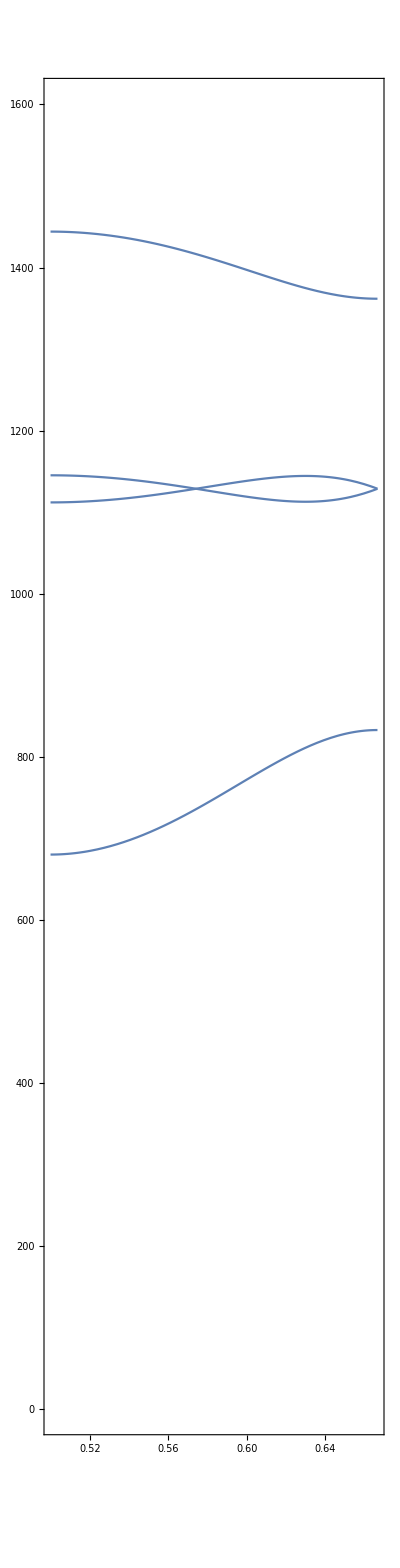

```mathematica
mk=Plot[omega[k,1-k],{k,1/2,2/3},Frame->True,PlotRangePadding->{{None,None},{1,1}},AspectRatio->6/Sqrt[2],PlotRange->{0,1600}](*M->K path*)
```

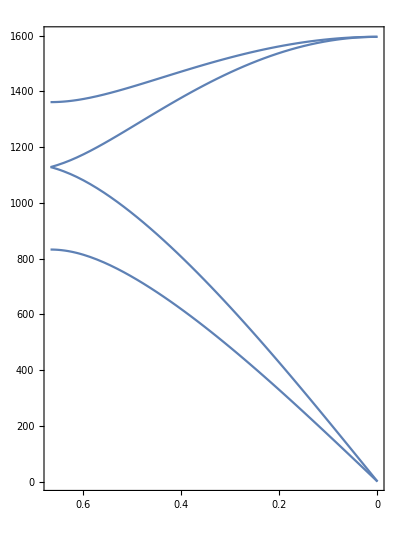

```mathematica
kg=Plot[omega[k,1/2k],{k,2/3,0},ScalingFunctions->{"Reverse",Identity}(*Invert horizontal axis*),Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,None}},PlotRangePadding->{{None,None},{1,1}},AspectRatio->3/Sqrt[5],PlotRange->{0,1600}](*K->Gamma path*)
```

```mathematica
(*Below is combine plots function,do not change this.*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

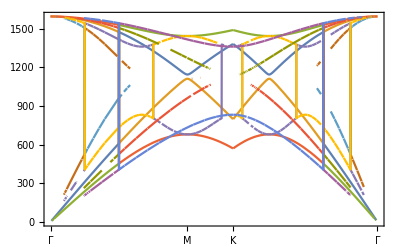

```mathematica
plotPath[{omega[k,k],omega[k,1-k],omega[k,1/2k]},{{{0,0},"Γ"},{{1/2,1/2},"M"},{{2/3,1/3},"K"},{{0,0},"Γ"}},Frame->True]
```